```mathematica
sol=ParametricNDSolve[{L'[r]==-Exp[-r]-(p)^2-L[r]^2,L[10^3]==I*p},L,{r,0,10},{p}]
```

{L→ParametricFunction[<>]}

```mathematica
G[p_]:=Gamma[1-ν] BesselJ[-ν,2]/. {ν->2 I p}
```

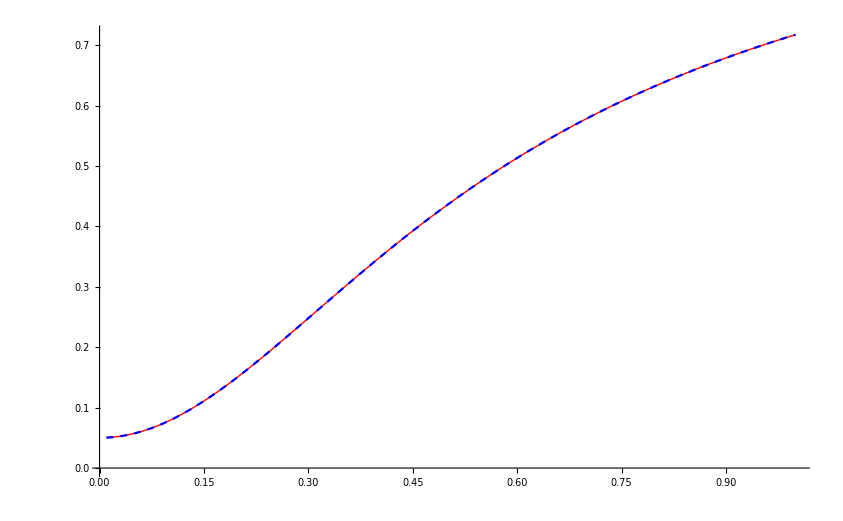

```mathematica
Plot[{Evaluate[q0/Im[L[q0][0]] /. sol] /. q0 -> p,Abs[G[q0]]^2/. q0->p},{p, 0.01, 1},PlotStyle->{{Red,Thick},{Blue,Dashed}}]
```

```mathematica
sol1=ParametricNDSolve[{L'[r]==(-Exp[-r])/r-(p)^2-L[r]^2,L[10^3]==I*p},L,{r,0,10},{p}]
```

{L→ParametricFunction[<>]}

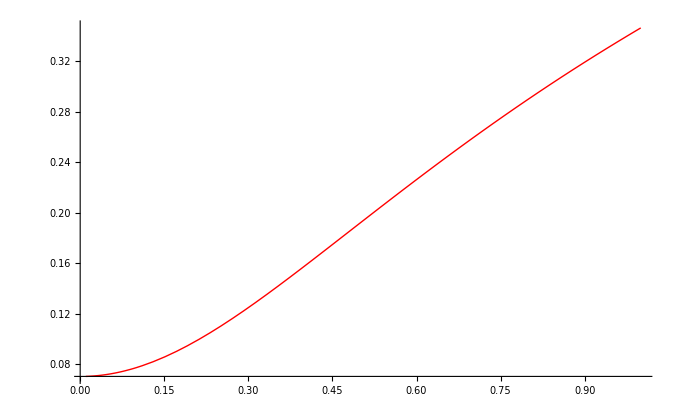

```mathematica
Plot[Evaluate[q0/Im[L[q0][0]] /. sol1] /. q0 -> p,{p, 0.01, 1},PlotStyle->{Red,Thick}]
```